## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"bouyancy.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"drag.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"visualizations.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Stability.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"COM.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"AVS.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"boats.m"}]]
```

```mathematica
boatboatboat[boat_]:=Quiet@Module[{thefront,theside,doesFloat,doesFloatFlat, trimAngle,stabilityPlot,stabilityAngles,bounds,floatHeight,area,area2,almostUp},
thefront=front/.boat;
theside=RotationMatrix[Pi/2,{0,0,1}].thefront;
doesFloat=Volume[region/.boat]Quantity[, ("Centimeters")^3]*Quantity[1, ("Grams")/("Centimeters")^3]>totalMass[boat]Quantity[, "Grams"];
doesFloatFlat=rightingArm[boat,thefront,N@10 Degree]>0&&rightingArm[boat,thefront,N@-10 Degree]<0;
trimAngle=Round[avs[boat,theside,0]*180/Pi]Quantity[, "AngularDegrees"];
doesFloatFlat=rightingArm[boat,thefront,N@10 Degree]>0&&rightingArm[boat,thefront,N@-10 Degree]<0 &&
Quantity[-5, "AngularDegrees"]<trimAngle<Quantity[5, "AngularDegrees"];
stabilityPlot=Plot[rightingArm[boat,thefront,θ],{θ,-Pi,Pi},PlotPoints->6, MaxRecursion->2];
stabilityAngles=DeleteDuplicates@Round[Table[avs[boat,thefront,i],{i,-Pi,Pi,Pi/3}]*180/Pi] Quantity[, "AngularDegrees"];
2
bounds=Round[RegionBounds[region/.boat]/.{min_,max_}:>max-min,0.1]Quantity[, "Centimeters"];
floatHeight=boatWaterline[boat,{0,0,1}];
area=underwaterArea[boat,{0,0,1},floatHeight];
area2=frontalArea[boat,{0,0,1},floatHeight,thefront];

almostUp=RotationMatrix[Quantity[5, "AngularDegrees"],thefront].{0,0,1};
Grid[{{Style[name/.boat,FontSize->60,FontFamily->"Purisa"],SpanFromLeft},
{showBoat[boat,almostUp],SpanFromLeft},
{"Is it a boat?","Boatboat."},
{"How big is it?",bounds},
{"Does it float?",doesFloat},
{"Stability curve",stabilityPlot},
{"Does it float flat?",doesFloatFlat},
{"Trim Angle?",trimAngle},
{"What's the AVS?",stabilityAngles},
{"How much is underwater?",area},
{"Cross-sectional area?",area2}
},Frame->All]
]
```

976.654

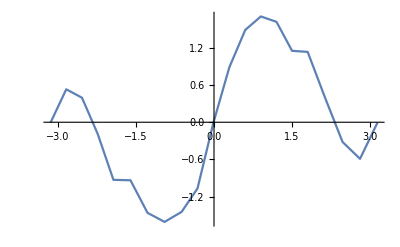
Bescadboat | 
-Graphics3D- | 
Is it a boat? | Boatboat.
How big is it? | bounds$86826
Does it float? | True
Stability curve | -Graphics-
Does it float flat? | True
Trim Angle? | 0 °
What's the AVS? | {-180 °,-133 °,-94 °,0 °,131 °,180 °}
How much is underwater? | 578.101 cm^2
Cross-sectional area? | 0

```mathematica
boatboatboat[Evaluate@scadboat]
```